```mathematica
Quit[]
```

## QCD

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[1,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[1,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[1,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.293951

0.30283

0.2923

0.394643

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
fudge = 4;
```

```mathematica
t=FindRoot[αs1Loop[mu]==0.214850,{mu,1}][[1,2]]
mb=FindRoot[t==fudge αs1Loop[t] mQ,{mQ,10000}][[1,2]]
a=t/(4 mb)
```

9.66044

11.2409

0.21485

```mathematica
t=FindRoot[αs2Loop[mu]==0.227325,{mu,1}][[1,2]]
mb=FindRoot[t==fudge αs2Loop[t] mQ,{mQ,10000}][[1,2]]
a=t/(4 mb)
```

3.72069

4.09182

0.227325

```mathematica
t=FindRoot[αs3Loop[mu]==0.222492,{mu,1}][[1,2]]
mb=FindRoot[t==fudge αs3Loop[t] mQ,{mQ,10000}][[1,2]]
a=t/(4 mb)
```

4.37666

4.91777

0.222492

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[1,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[1,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[1,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf[Mt,6]-(αsNf[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.09

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf[Mb,4]-(αsNf[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.296

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf[Mc,3]-(αsNf[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.338

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335424

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.337099

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
ΛQCD4Loop[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ4Loop[Q_,f_]:=Log[Q^2/ΛQCD4Loop[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[1,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[1,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[1,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.293951

0.304349

0.322415

0.270092

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
ΛQCD4Loop[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.293951

0.304349

0.322415

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

```mathematica
nfTab={3,3,3,3,4,5,5};
```

```mathematica
ΛQCD4LoopTab=Table[ΛQCD4Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.338,0.338,0.338,0.338,0.296,0.213,0.213}

{0.335424,0.335424,0.335424,0.335424,0.299152,0.217435,0.217435}

{0.386001,0.386001,0.386001,0.386001,0.332194,0.229911,0.229911}

{0.337099,0.337099,0.337099,0.337099,0.122648,0.0893248,0.0893248}

```mathematica
μGeV4LoopTab=μoΛTab ΛQCD4LoopTab
```

{0.355789,0.450667,0.676,1.352,5.92,21.3,213.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.353077,0.447231,0.670847,1.34169,5.98303,21.7435,217.435}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.406317,0.514668,0.772002,1.544,6.64387,22.9911,229.911}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.354841,0.449466,0.674199,1.3484,2.45297,8.93248,89.3248}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6578.04,10.0428,0.878876,0.373108,0.204763,0.152134,0.105092}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{32.1426,3.28903,0.875133,0.37608,0.200221,0.150653,0.104278}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{13.6106,2.42675,1.00719,0.503596,0.251685,0.177962,0.118641}

```mathematica
(* or if we dont freeze < 1 GeV *)
```

```mathematica
Table[αs[μGeV4LoopTab[[n]]],{n,Length[nfTab]}]
```

{0.382561,0.382561,0.382561,0.33475,0.203669,0.151919,0.105238}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6578.04,10.0428,0.878876,0.373108,0.204763,0.152134,0.105092}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{32.1426,3.28903,0.875133,0.37608,0.200221,0.150653,0.104278}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{13.6106,2.42675,1.00719,0.503596,0.251685,0.177962,0.118641}

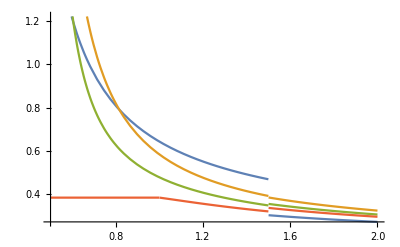

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

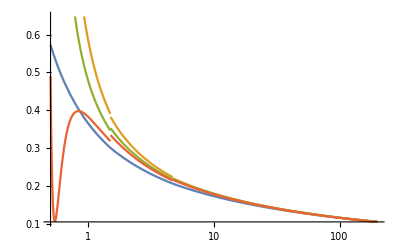

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

## dQCD

### Nc=3

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->0
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N))/.Nf->0
αsNf2Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->0
αsNf1Loop[Q_,f_]:=(1/(β0N LQ[Q,f]))/.Nf->0
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[1,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[1,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[1,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.213463

0.224623

0.210555

0.298972

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->0
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->0
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->0
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->0
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[1,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[1,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[1,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf[Mt,6]-(αsNf[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.09

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf[Mb,4]-(αsNf[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.296

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf[Mc,3]-(αsNf[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.338

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.225584

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0004188

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.462877

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.657773

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.246231

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.246231

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.246231

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.246231

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0695787

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0695787

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.0695787

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.462877

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
ΛQCD4Loop[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ4Loop[Q_,f_]:=Log[Q^2/ΛQCD4Loop[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[1,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[1,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[1,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.294778

0.387449

0.250593

0.224503

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
ΛQCD4Loop[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.294778

0.387449

0.250593

0.224503

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

3.2406

6.09185

21.5583

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

20.8348

19.0878

67.5494

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

413897.

703.974

2491.28

```mathematica
nfTab={3,3,3,3,4,5,5};
```

```mathematica
ΛQCD4LoopTab=Table[ΛQCD4Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.338,0.338,0.338,0.338,0.296,0.213,0.213}

{0.657773,0.657773,0.657773,0.657773,0.462877,0.225584,0.225584}

{0.246231,0.246231,0.246231,0.246231,0.246231,0.246231,0.246231}

{0.462877,0.462877,0.462877,0.462877,0.0695787,0.0695787,0.0695787}

```mathematica
μGeV4LoopTab=μoΛTab ΛQCD4LoopTab
```

{0.355789,0.450667,0.676,1.352,5.92,21.3,213.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.692393,0.877031,1.31555,2.63109,9.25754,22.5584,225.584}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.25919,0.328308,0.492461,0.984923,4.92461,24.6231,246.231}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.487239,0.617169,0.925754,1.85151,1.39157,6.95787,69.5787}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6611.89,10.0945,0.883398,0.330538,0.184817,0.152134,0.0637084}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{22.521,182.517,0.371225,0.257709,0.224644,0.151436,0.119957}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{13.6106,2.42675,1.00719,0.229782,0.634244,0.177962,0.118641}

```mathematica
(* or if we dont freeze < 1 GeV *)
```

```mathematica
Table[αs[μGeV4LoopTab[[n]]],{n,Length[nfTab]}]
```

{0.387075,0.387075,0.387075,0.3387,0.203669,0.151919,0.105185}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6611.89,10.0945,0.883398,0.330538,0.184817,0.152134,0.0637084}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{22.521,182.517,0.371225,0.257709,0.224644,0.151436,0.119957}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{13.6106,2.42675,1.00719,0.229782,0.634244,0.177962,0.118641}